```mathematica
g=9.8; (*grav. constant*)

x0=0; (*20 degrees*)
vx0 = 3; 
y0=0;
vy0=3;
vt=10;(*starting from rest*)
(*ϕ=y;
t=x;*)
ode1={x''[t]==-(g x'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2],x[0]==x0,x'[0]==vx0};

ode2={y''[t]==-g(l+(y'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2]),y[0]==y0,y'[0]==vy0};

sol=NDSolve[{ode1,ode2},{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

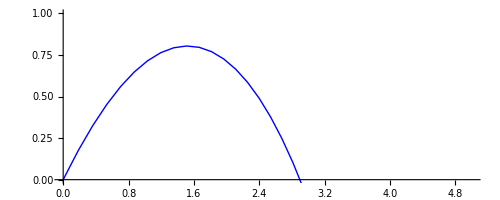

-Graphics-

```mathematica
myplot1=ParametricPlot[Evaluate[{x[t],y[t]}/.sol,{t,0,200},PlotStyle->RGBColor[0,0,1],PlotRange->{{0,5},{0,1}}] ]

Show[myplot1]
```

```mathematica
Manipulate[
g=9.8;
x0=0;
y0=0;
vx0=Cos(θ)/v0;
vy0=Sin(θ)/v0;

ode1={x''[t]==-(g x'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2],x[0]==x0,x'[0]==vx0};

ode2={y''[t]==-g(l+(y'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2]),y[0]==y0,y'[0]==vy0};

Module[{result=NDSolve[{ode1,ode2},{x,y},{t,0,200}]},
ParametricPlot[Evaluate[{x[t],y[t]}/.sol,{t,0,200},PlotStyle->RGBColor[0,0,1],PlotRange->{{0,5},{0,1}}] ],
ImageSize->{500,300}]],{{v0,"v0"},0,10,Appearance->"Labeled"},{{θ,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},{{vt,"vt"},0,100.,Appearance->"Labeled"}
```